```mathematica
de = v*t - b*t^2/2 + (v-b*t)^2/p
do = vo^2/(2*p)
```

-(b t^2)/2+t v+(-b t+v)^2/p

vo^2/(2 p)

```mathematica
result = Simplify[Solve[de== do+g, b]]
```

{{b→(p t+4 v-√(16 g p+p^2 t^2-8 p t v+8 vo^2))/(4 t)},{b→(p t+4 v+√(16 g p+p^2 t^2-8 p t v+8 vo^2))/(4 t)}}

```mathematica
vals = {vo->25,v->30,g->20,p->20,t->0.5}
```

{vo→25,v→30,g→20,p→20,t→0.5}

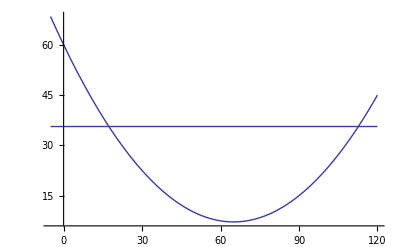

```mathematica
Plot[{de,do+g}/.vals,{b,-5,120}]
```